# Практикум №1 . Приемы работы в Mathematica

Выполнил студент ММФ  БГУ
КМ, 1 к, 3 гр . Шпак А . В .
  21 сентября 2021

## 2. Ввод и отображение математических выражений

### Задание 2.1

Введите с клавиатуры выражение y (x), представленное ниже. Вариант 9.

```mathematica
ⅇ^(a x)(1/(2 a)+(a Cos[2 b x]+2 b Sin[2 b x])/(2 (a^2+4 b^2)))
```

ⅇ^(a x) (1/(2 a)+(a Cos[2 b x]+2 b Sin[2 b x])/(2 (a^2+4 b^2)))

### Задание 2.2

Ознакомьтесь с различными форматами представления выражения. Используйте выражение y(x), введенное при выполнении задания 2.1.
Комментарии к решению: мы можем осуществлять ввод данных в различных форматах, среди которых выделяют InputForm (Ctrl+Shift+I), TraditionalForm (Ctrl+Shift+T), StandardForm (Ctrl+Shift+N) и FullForm.
StandardForm – двумерная структура выражения. Получаем с помощью  палитры ввода Palettes, комбинации «горячих» клавиш.
InputForm – одномерная структура, в которой символы располагаются последовательно друг за другом. Получаем с помощью простого ввода с клавиатуры.
TraditionalForm – отображение выражения происходит в традиционной математической нотации.
FullForm – представление выражения в том виде, в котором с ним работает ядро системы.
Вывод о том, как строится полная форма выражения я сделал во второй лабораторной.

ⅇ^(a x) (1/(2 a)+(a Cos[2 b x]+2 b Sin[2 b x])/(2 (a^2+4 b^2)))

Times[Power[E,Times[a,x]],Plus[Times[Rational[1,2],Power[a,-1]],Times[Rational[1,2],Power[Plus[Power[a,2],Times[4,Power[b,2]]],-1],Plus[Times[a,Cos[Times[2,b,x]]],Times[2,b,Sin[Times[2,b,x]]]]]]]

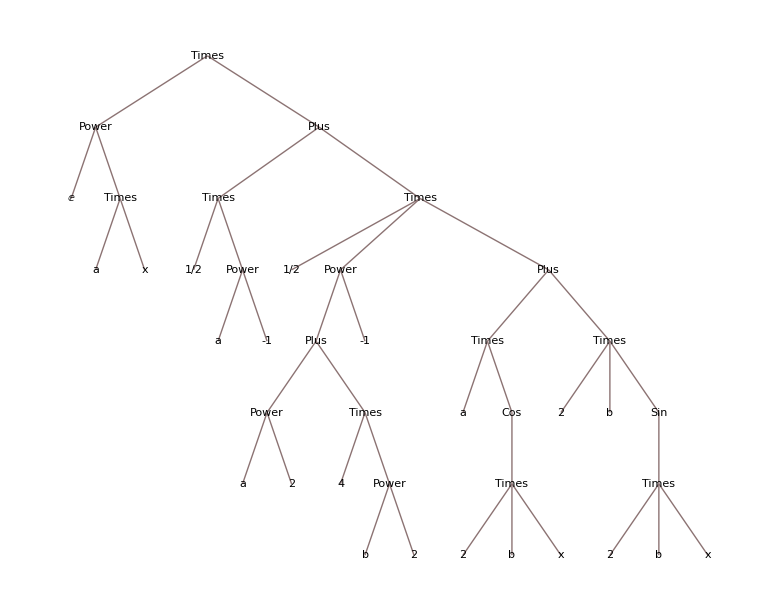

```mathematica
ⅇ^(a x) ((a Cos[2 b x]+2 b Sin[2 b x])/(2 (a^2+4 b^2))+1/(2 a))
ⅇ^(a x) ((a Cos[2 b x]+2 b Sin[2 b x])/(2 (a^2+4 b^2))+1/(2 a))//FullForm
ⅇ^(a x) ((a Cos[2 b x]+2 b Sin[2 b x])/(2 (a^2+4 b^2))+1/(2 a))//TreeForm
```

### Задание 2.3

Для выражения y(x), введённого при выполнении задания 2.1, вычислите его производную по переменной x и упростите ее. Используйте функции семейства Simplify.

```mathematica
func=ⅇ^(a x) ((a Cos[2 b x]+2 b Sin[2 b x])/(2 (a^2+4 b^2))+1/(2 a))
D[func,x]
myExpr=FullSimplify[D[func,x]]
?myExpr
```

ⅇ^(a x) (1/(2 a)+(a Cos[2 b x]+2 b Sin[2 b x])/(2 (a^2+4 b^2)))

(ⅇ^(a x) (4 b^2 Cos[2 b x]-2 a b Sin[2 b x]))/(2 (a^2+4 b^2))+a ⅇ^(a x) (1/(2 a)+(a Cos[2 b x]+2 b Sin[2 b x])/(2 (a^2+4 b^2)))

ⅇ^(a x) Cos[b x]^2

## 3. Ввод и отображение математических выражений

### Задание 3.1

В заданном квадратном трехчлене, выражение вида ax^2 + bx + c ≠ 0, выделите полный квадрат относительно переменной x, введя подходящую замену переменных.
Результат вычисления ассоциируйте с символом Result.
Вариант 9. 
Комментарии к решению: вручную полный квадрат я выделяю следующим образом
-Graphics-
Насчёт решения в Mathematica однозначно я не могу утверждать, мне трудно подобрать такую замену, чтобы получился пример с явным видом выделенного квадрата. Возможно, я не до конца осознаю смысл фразы “выделение полного квадрата”, потому просто выполняю по примеру.

```mathematica
Result=7 x^2+18  x+5 /.x->(t-18/2)/7
%//Simplify
?Result
```

5+18/7 (-9+t)+1/7 (-9+t)^2

1/7 (-46+t^2)

### Задание 3.2

Поработайте с выражением, ассоциированным с символом Result, которое Вы получили при выполнении задания 3.1, следующим образом: представьте Result в виде суммы, вычислите полученное количество слагаемых, затем – в виде произведения, вычислите количество множителей.
Используйте функции Factor, Expand, Length. Полученные сумму и произведение ассоциируйте с соответствующими символами ResSum, ResProduct.
Комментарии к решению: с помощью функции Factor, я представляю своё выражение в виде произведения скобок с другими выражениями. Так как в моём случае символ Result уже представляет собой некоторое произведение, то, предполагаю, что преобразований функция не производит. Затем функцией Length я считаю количество аргументов выражения. В моём случае на первом уровне содержится два выражения и голова Times. Потому в результате я и получаю выовод: 2.
Следующим этапом я считаю количество аргументов результата выполнения другой функции - Expand -, которая раскрывает скобки у моего выражения, получая Sum в виде head’а и два составных выражения. В итоге получаю также 2.

```mathematica
Factor[Result]
ResProduct=Length[Factor[Result]]
Expand[Result]
ResSum=Length[Expand[Result]]
```

1/7 (-46+t^2)

2

-46/7+t^2/7

2

### Задание 3.3

Выясните разницу в практическом использовании атомарных объектов типа Integer и Real. Выводы расположите в текстовой ячейке.
Комментарии к решению: мне трудно просто взять и объяснить такую разницу в вычислениях. Я просто приведу свои наблюдения и по возможности постараюсь прийти к какому-нибудь выводу. 
У обоих выражений я вывожу их полную форму, так же анализирую атомарные выражения и структуру в виде дерева с помощью чистой функции. Действительно, так как подстановка меняется с типа Integer на тип Real, то и атомарные выражения, подвергавшиеся взаимодействию с вещественным типом становятся так же типом вещественным. Насколько мне известно, в современных ЯП такой процесс называется неявным приведением типов, который система производит где-то “под капотом”, а мы видим только результат. В явном виде это могло бы выглядеть, например, вот так: (написано на псевдокоде) ToReal(7) * 18. Но, так как я не знаю, как именно работает ядро Mathematica, приписывать именно ей такой способ работы было бы довольно смелым утверждением. Но как факт мы имеем результат проверки head’ов атомарных аргументов - в новом выражении мы получаем тип Real в результате вычислений. То же видно и на структурах-деревьях. Новое выражение значительно меняет свой вид в отличие от оригинала, что, как мне кажется, обусловленно особенностью внутреннего устройством ядра, потому что подсчёт значений происходит в Real. 
Уточнение. После замены всех атом в подстановке я получаю выражение идентичное исходному, за ислючением только того, что атомы представлены типом Real, но само выражение выглядит адекватно. Значит мои предыдущие выводы могут не соответствовать действительности и я предполагаю, что вариант с подстановкой одного атома типа Real может порождать конфликты в системе, которые и выливаются в довольно странный результат, записанный в символе ResultReal. Вывод: если и делать выражение типом Real, то делать все его атомы.

1/7 (-46+t^2)

{{Rational,1/7},{Integer,-46},{Symbol,t},{Integer,2}}

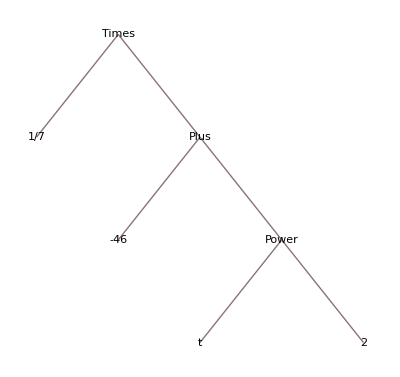

0.142857 (-46.+3.10862×10^-15 t+t^2)

{{Real,0.142857},{Real,-46.},{Real,3.10862×10^-15},{Symbol,t},{Symbol,t},{Integer,2}}

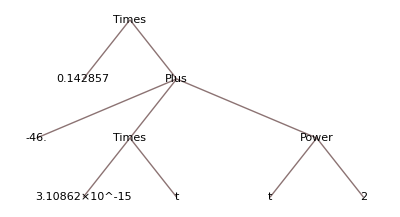

-6.57143+0.142857 t^2

{{Real,-6.57143},{Real,0.142857},{Symbol,t},{Integer,2}}

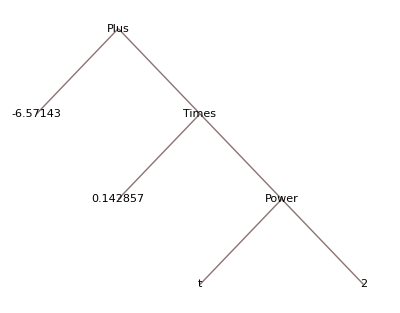

```mathematica
(*Вывожу свойства, соответствующие исходному выражению*)
Result=7 x^2+18  x+5 /.x->(t-18/2)/7//Simplify
{Head[#],#}&/@Level[Result,{-1}]
TreeForm[Result]
(*Вывожу свойства, соответствующие выражению с подстановкой Real*)
ResultReal=7 x^2+18  x+5 /.x->(t-18./2)/7//Simplify
{Head[#],#}&/@Level[ResultReal,{-1}]
TreeForm[ResultReal]
(*Вывожу свойства, соответствующие выражению с подстановкой Real для всех атомов*)
ResultRealAll=7. x^2+18.  x+5. /.x->(t-18./2.)/7.//Simplify
{Head[#],#}&/@Level[ResultRealAll,{-1}]
TreeForm[ResultRealAll]
```

### Задание 3.4

Укажите замену переменных (постройте выражение – локальную подстановку), позволяющую выделить полный квадрат в квадратном трехчлене общего вида ax^2 + bx + c, a ≠ 0.
Комментарии к решению: насколько я понял, я описал функцию с телом, которое создаёт замену для x и набором параметров. Ну и проверил работу функции на моём выражении. В результате всё получилось, как и в предыдущих заданиях. Тогда я решил проверить, как ведут себя параметры, если я не указываю им в соответствие аргументы, принимают ли они значения по умолчанию? Для проверки использовал функцию Trace. Ответ убил - не принимают, хотя изначально мне показалось, что так это будет работать, ведь для Quadratic[x^2+18  x ] параметр c принял значение нуля, а параметр a - единицы. Но в следующих примерах я опровергаю своё предположение. Просто выражение x^2+18  x  всё ещё остаётся квадратным, в отличие от остальных. К слову для других значений коэффициентов всё работает как нужно

```mathematica
Quadratic[expr:a_. x^2+b_.x+c_.]:=(a x^2+b x+c/.x->(t-18/2)/7)
Quadratic[7 x^2+18  x+5 ]//Simplify
Quadratic[x^2+18  x ]
Quadratic[x^2]
Quadratic[x^2+18  ]
Trace[Quadratic[x^2+18  x ]//Simplify]
Trace[Quadratic[x^2]]
Trace[Quadratic[x^2+18  ]]
Quadratic[4 x^2+10  x-50 ]//Simplify
```

1/7 (-46+t^2)

18/7 (-9+t)+1/49 (-9+t)^2

Quadratic[x^2]

Quadratic[18+x^2]

{{{x^2+18 x,18 x+x^2},Quadratic[18 x+x^2],1 x^2+18 x+0/.x→1/7 (t-18/2),{{1 x^2,x^2},x^2+18 x+0,x^2+18 x,18 x+x^2},{{{{{{1/2,1/2},18/2,9},-9,-9},t-9,-9+t},{1/7,1/7},1/7 (-9+t),1/7 (-9+t)},x→1/7 (-9+t),x→1/7 (-9+t)},18 x+x^2/.x→1/7 (-9+t),18/7 (-9+t)+(1/7 (-9+t))^2,{18/7 (-9+t),18/7 (-9+t),18/7 (-9+t),18/7 (-9+t)},{(1/7 (-9+t))^2,1/49 (-9+t)^2},18/7 (-9+t)+1/49 (-9+t)^2},Simplify[18/7 (-9+t)+1/49 (-9+t)^2],1/49 (-1053+108 t+t^2)}

{}

{{x^2+18,18+x^2},Quadratic[18+x^2]}

2/49 (-1378-t+2 t^2)

### Задание 3.5

Постройте график функции, заданной соотношением вида y(x)= ax^2 + bx + c, a ≠ 0, Ваш вариант задания 3.1. Используйте функцию Plot. Измените цвет, толщину, начертание линии, отобразите графический объект с/без осей координат, легенды и т.п. Для справки используйте выражение Options[Plot] и клавишу F1.

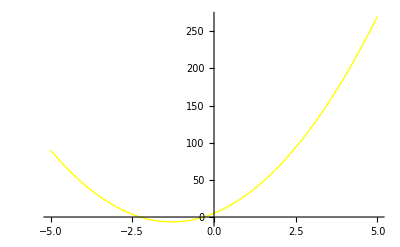

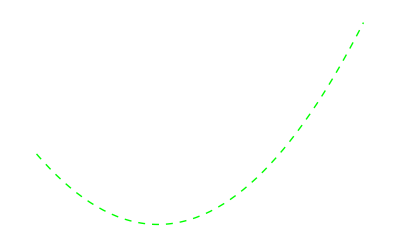

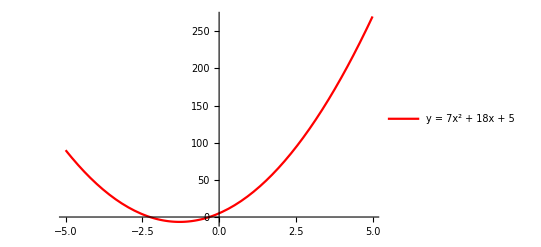

```mathematica
Plot[7 x^2+18  x+5 ,{x, -5,5}, PlotStyle->{Thick, Yellow}]
Plot[7 x^2+18  x+5 ,{x, -5,5}, PlotStyle->{Thick, Green, Dashed}, Axes->False]
Plot[7 x^2+18  x+5 ,{x, -5,5}, PlotStyle->{Thin, Red}, PlotLegends->Placed[{"y = 7x^2 + 18x + 5 "},Above]]
```

## 4. Решение уравнений, неравенств и их систем.

### Задание 4.1

Решите заданную систему уравнений несколькими способами, используя:
1) возможности графики,
2) встроенные функции для решения систем уравнений.
Вариант 9.
Комментарии к решению: аналитически посчитал на листочке
-Graphics-
Ответ совпал как с графиком, так и с решением функции Solve.

{{x→8/7,y→3/7},{x→4/7,y→5/7}}

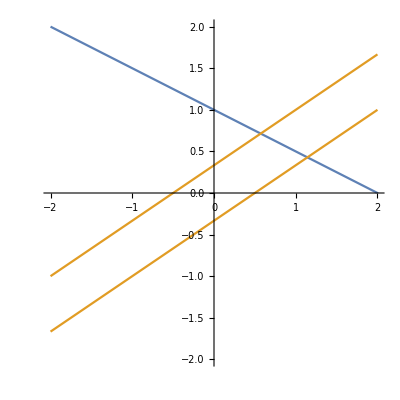

```mathematica
Solve[{x+2 y==2,Abs[2 x-3 y]==1},{x,y}]
ContourPlot[{x+2 y==2,Abs[2 x-3 y]==1},{x,-2,2},{y,-2,2},Axes->True,Frame->False]
```

### Задание 4.2

Решите заданное уравнение относительно переменной x, при условии, что вторая переменная является вещественным параметром. Используйте функции Solve и Reduce. Сформулируйте выводы об использовании этих функций. В отдельной текстовой ячейке представьте традиционное математическое решение заданного уравнения, используйте возможности двумерного ввода формул.
Вариант 9.
Комментарии к решению: в задании попросили оформить ручками, что ж поделать
(x^2+(3 b-1) x+2 b^2-2)/(x^2-3 x-4)=0
Считаю, что сам b>0.
1) Знаменатель не равен нулю.
x^2-3 x-4!=0
Решаю квадратное уравнение.
x_1!=4;
x_2!=-1;
2) Числитель приравниваю к нулю и решаю квадратное уравнение относительно x.
x^2+(3 b-1) x+2 b^2-2==0
D=(3 b-1)^2-4(2 b^2-2)=9 b^2+1-6b-8 b^2+8=b^2-6b+9=(b-3)^2
Дискриминант положительный, получаю корни:
x_1=(-3b+1-√((b-3)^2))/2=(-3b+1-b+3)/2=(-4b+4)/2=2-2b;
x_1=(-3b+1+√((b-3)^2))/2=(-3b+1+b-3)/2=(-2b-2)/2=-b-1;
Корни совпали с решением функцией Solve. При этом функция работает отлично, в отличие от Reduce, который выводит странные вещи.

```mathematica
(x^2+(3 b-1) x+2 b^2-2)/(x^2-3 x-4)==0
Solve[(x^2+(3 b-1) x+2 b^2-2)/(x^2-3 x-4)==0,x]
```

(-2+2 b^2+(-1+3 b) x+x^2)/(-4-3 x+x^2)==0

{{x→-1-b},{x→-2 (-1+b)}}

### Задание 4.3

Продемонстрируйте графически зависимость решения уравнения (задание 4.2) от значений параметра. Вариант 9.
Комментарии к решению: я не понял, как работает метод решения предложенный в примере. Мы строим прямые, параллельные оси абсцисс, а точки пересечения этих прямых и P(x) являются решениями... И я не знаю, каким образом тут хоть как-то приплести функцию Reduce.

(-2+2 b^2+(-1+3 b) x+x^2)/(-4-3 x+x^2)==0

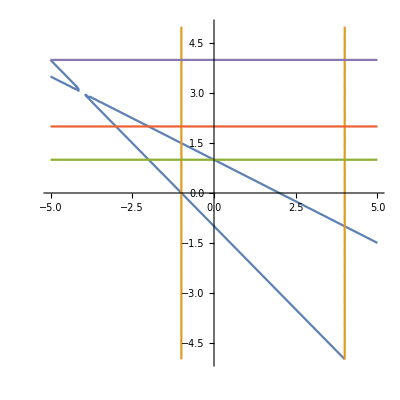

(x==-1-b&&5 b+b^2≠0)||(x==-2 (-1+b)&&-3-b+2 b^2≠0)

```mathematica
(x^2+(3 b-1) x+2 b^2-2)/(x^2-3 x-4)==0
ContourPlot[{-2+2 b^2+(-1+3 b) x+x^2==0, -4-3 x+x^2==0, b==1,b==2,b==4},{x,-5,5},{b,-5,5}, Axes->True, Frame->False]
Reduce[(x^2+(3 b-1) x+2 b^2-2)/(x^2-3 x-4)==0,x]
```

```mathematica
Solve[(x^2+(3 b-1) x+2*b^2-2)/(x^2-3 x-4)==0]
```

{{x→2-2 b},{x→-1-b}}

### Задание 4.4

Решите заданное неравенство относительно переменной x, при условии, что вторая переменная является вещественным параметром. Используйте функции Solve и Reduce. Сформулируйте выводы об использовании этих функций. Вариант 9.

```mathematica
Solve[x^2-2 x+1+a>0,x]
Reduce[x^2-2 x+1+a>0,x]
```

Solve::fdimc: When parameter values satisfy the condition a>0||a<0||a<0, the solution set contains a full-dimensional component; use Reduce for complete solution information.

{}

x∈ℝ&&((a≤0&&(x<1-√-a||x>1+√-a))||a>0)

### Задание 4.5

Продемонстрируйте графически зависимость решения неравенства (задание 4.3) от значений параметра. Запишите ответ при каждом значении параметра. Вариант 9.
Комментарии к решению: всё ещё не разобрался... Строю параболу, беря просто уравнение x^2-2 x+1+a==0. При этом пытаюсь реализовать предложенный метод, согласно которому строю прямую, параллельную оси абсцисс, потом вдоль(?) этой прямой двигаю свои другие прямые и точки пересечения с P(x) и будут решением. Но ведь у нас неравенство, в котором знак строгий... И мы меняем параметр a, разве не должен вместе с ним меняться график параболы?

1+a-2 x+x^2>0

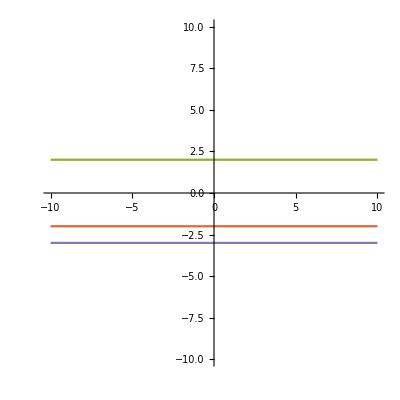

x∈ℝ&&((a≤0&&(x<1-√-a||x>1+√-a))||a>0)

```mathematica
x^2-2 x+1+a>0
ContourPlot[{(x-1)^2==0,c==-a,a==2,a==-2,a==-3},{x,-10,10},{a,-10,10}, Axes->True, Frame->False]
Reduce[x^2-2 x+1+a>0,x]
```